```mathematica
FullSimplify[4π (1-Exp[-Subscript[E, ν]/T])/(Subscript[E, ν]^3 Sqrt[T])a c/(4 π)15/π^4 Subscript[E, ν]^3/(Exp[Subscript[E, ν]/T]-1)]
```

(15 a c ⅇ^(-ⅇ_ν/T))/(π^4 √T)

```mathematica
TeXForm[%]
```

\frac{15 a c e^{-\frac{e_{\nu }}{T}}}{\pi ^4 \sqrt{T}}

```mathematica
Assuming[T>0,Integrate[(15 a c ⅇ^(-Subscript[ⅇ, ν]/T))/(π^4 √T),{Subscript[E, ν],0,∞}]]
```

(15 a c √T)/π^4

```mathematica
TeXForm[%]
```

\frac{15 a c \sqrt{T}}{\pi ^4}

```mathematica
Normal[Series[T[t]^4,{t,0,2}]]
```

T[0]^4+4 t T[0]^3 T'[0]+2 t^2 T[0]^2 (3 T'[0]^2+T[0] T''[0])

```mathematica
FullSimplify[(-u+Sqrt[u^2-4 v ])/2/.{u-> Sqrt[y0] ,v-> (y0^(3/2)-A)/(2 Sqrt[y0])}]/.{A->Cv/a,y0-> Subscript[y, 0]}
```

1/2 (√((2 Cv)/(a √y_0)-y_0)-√y_0)

```mathematica
FullSimplify[(-u+Sqrt[u^2-4 v ])/2/.{u-> Sqrt[y0] ,v-> (y0^(3/2)-A)/(2 Sqrt[y0])}]/.{A->Cv/a,y0-> Subscript[y, 0]}
```

1/2 (√((2 Cv)/(a √y_0)-y_0)-√y_0)

```mathematica
%/.{a-> 4/300,Cv-> 0.3}
```

1/2 (√(45./(√y_0)-y_0)-√y_0)

```mathematica
TeXForm[%]
```

\frac{1}{2} \left(\sqrt{\frac{2 \text{Cv}}{a \sqrt{y_0}}-y_0}-\sqrt{y_0}\right)

```mathematica
FullSimplify[u^2-4 w /.{u-> Sqrt[y0] ,w->y0- (y0^(3/2)-A)/(2 Sqrt[y0])}]/.{A->Cv/a,y0-> Subscript[y, 0]}
```

-(2 Cv)/(a √y_0)-y_0

```mathematica
TeXForm[%]
```

-\frac{2 \text{Cv}}{a \sqrt{y_0}}-y_0

```mathematica
y0V= CubeRoot[-Q/2 +Sqrt[(Q/2)^2 + (P/3)^3]]+CubeRoot[-Q/2 -Sqrt[(Q/2)^2 + (P/3)^3]]
```

(-Q/2-√(P^3/27+Q^2/4))^(1/3)+(-Q/2+√(P^3/27+Q^2/4))^(1/3)

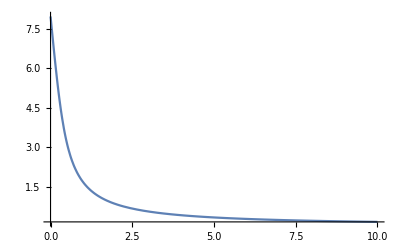

```mathematica
Plot[y0V/.{P-> 4 x/(4/300),Q-> -0.3^2/(4/300)^2},{x,0,10},PlotRange->All]
```

```mathematica
FullSimplify[ CubeRoot[-Q/2 +Sqrt[(Q/2)^2 + (P/3)^3]]+CubeRoot[-Q/2 -Sqrt[(Q/2)^2 + (P/3)^3]]/.{P-> 4 Subscript[E, r0]/a,Q-> -Subscript[C, v]^2/a^2}]
```

(C_v^2/(2 a^2)-√(C_v^4/(4 a^4)+(64 ⅇ_r0^3)/(27 a^3)))^(1/3)+(C_v^2/(2 a^2)+√(C_v^4/(4 a^4)+(64 ⅇ_r0^3)/(27 a^3)))^(1/3)

```mathematica
Series[CubeRoot[-Q/2 +Sqrt[(Q/2)^2 + (P/3)^3]]+CubeRoot[-Q/2 -Sqrt[(Q/2)^2 + (P/3)^3]],{P,0,2}]
```

Piecewise[{{1/2 (2^(2/3) (-Q+Abs[Q])^(1/3)-2^(2/3) (Q+Abs[Q])^(1/3))+O[P]^3, (-9 Q+√3 √(4 P^3+27 Q^2)<0||9 Q+√3 √(4 P^3+27 Q^2)>0)&&-9 Q+√3 √(4 P^3+27 Q^2)≥0}, {(-Q)^(1/3)+((P^3/Q)^(1/3) P)/(3 P)+O[P]^3, 9 Q+√3 √(4 P^3+27 Q^2)≤0&&-9 Q+√3 √(4 P^3+27 Q^2)≥0}, {-Q^(1/3)+P/(3 Q^(1/3))+O[P]^3, True}}]